## Chapter::11 Fourier Series,Integrals,and Transforms

```mathematica
f = a0+Sum[anCos[n Pi x/L]+bn Sin[n Pi x/L],{x,1,Infinity}]
```

a0+∑_(x=1)^∞ (anCos[(n π x)/L]+bn Sin[(n π x)/L])

```mathematica
Clear[f]
```

```mathematica
a[0]=1/(2L)Integrate[f[x],{x,-L,L}]
```

(∫_-L^L f[x]ⅆx)/(2 L)

```mathematica
a[n]=1/L Integrate[f[x] Cos[n Pi x/L],{x,-L,L}]
```

(∫_-L^L Cos[(n π x)/L] f[x]ⅆx)/L

```mathematica
b[n]=1/L Integrate[f[x] Sin[ n Pi x/L],{X,-L,L}]
```

2 f[x] Sin[(n π x)/L]

## 11.1 Functions Of Period 2 PI Even Functions Gibbs Phenomenon::

```mathematica
a0 =1/(2Pi)Integrate[k,{x,-Pi/2,Pi/2}]
```

k/2

```mathematica
an =1/Pi Integrate[k Cos[n x],{x,-Pi/2,Pi/2}]
```

(2 k Sin[(n π)/2])/(n π)

```mathematica
bn =1/Pi Integrate[k Sin[n x],{x,-Pi/2,Pi/2}]
```

0

```mathematica
Table[an,{n,1,0}]
```

{}

```mathematica
An =an/.k-> 1
```

(2 Sin[(n π)/2])/(n π)

```mathematica
S1 =1/2 +Sum[An Cos[n x],{n,1,1}]
```

1/2+(2 Cos[x])/π

```mathematica
S3 =1/2 +Sum[An Cos[n x],{n,1,3}]
```

1/2+(2 Cos[x])/π-(2 Cos[3 x])/(3 π)

```mathematica
S5 =1/2 +Sum[An Cos[n x],{n,1,5}]
```

1/2+(2 Cos[x])/π-(2 Cos[3 x])/(3 π)+(2 Cos[5 x])/(5 π)

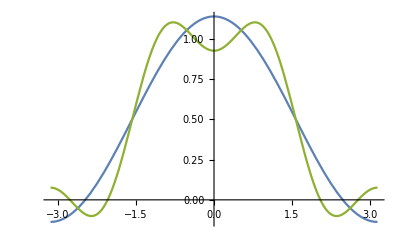

```mathematica
p1 =Plot[{S1,S2,S3},{x,-Pi,Pi}]
```

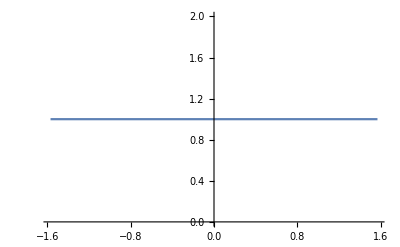

```mathematica
P2 =Plot[1,{x,-Pi/2,Pi/2}]
```

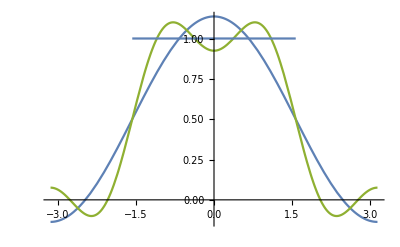

```mathematica
Show[p1,P2]
```

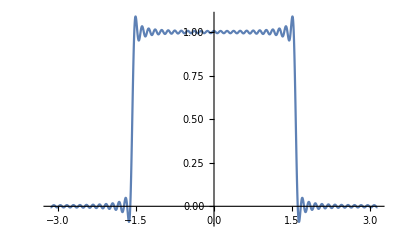

```mathematica
Plot[1/2+Sum[An Cos[n x],{n,1,50}],{x,-Pi,Pi}]
```

## Functions Of Arbitrary Period Odd Functions::

```mathematica
p =Line[{{-3,-1},{-1,1},{-1,-1},{1,1},{1,-1},{3,1}}]
```

Line[{{-3,-1},{-1,1},{-1,-1},{1,1},{1,-1},{3,1}}]

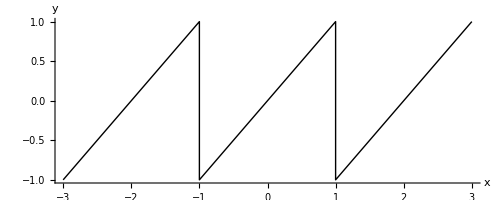

```mathematica
Show[Graphics[p],Axes->True,AxesLabel->{x,y},AspectRatio->Automatic]
```

```mathematica
a0 =1/2Integrate[x,{x,-1,1}]
```

0

```mathematica
an1 = 1/2Integrate[x Cos[n Pi x],{x,-1,1}]
```

0

```mathematica
bn1 =Integrate[x Sin[n Pi x],{x,-1,1}]
```

(-2 n π Cos[n π]+2 Sin[n π])/(n^2 π^2)

```mathematica
Table[bn1,{n,1,0}]
```

{}

```mathematica
S11 =Sum[bn1 Sin[n Pi x],{n,1,1}]
```

(2 Sin[π x])/π

```mathematica
S12 =Sum[bn1 Sin[n Pi x],{n,1,2}]
```

(2 Sin[π x])/π-Sin[2 π x]/π

```mathematica
S13 =Sum[bn1 Sin[n Pi x],{n,1,3}]
```

(2 Sin[π x])/π-Sin[2 π x]/π+(2 Sin[3 π x])/(3 π)

```mathematica
s5 =Sum[bn1 Sin[n Pi x],{n,1,50}]
```

(2 Sin[π x])/π-Sin[2 π x]/π+(2 Sin[3 π x])/(3 π)-Sin[4 π x]/(2 π)+(2 Sin[5 π x])/(5 π)-Sin[6 π x]/(3 π)+(2 Sin[7 π x])/(7 π)-Sin[8 π x]/(4 π)+(2 Sin[9 π x])/(9 π)-Sin[10 π x]/(5 π)+(2 Sin[11 π x])/(11 π)-Sin[12 π x]/(6 π)+(2 Sin[13 π x])/(13 π)-Sin[14 π x]/(7 π)+(2 Sin[15 π x])/(15 π)-Sin[16 π x]/(8 π)+(2 Sin[17 π x])/(17 π)-Sin[18 π x]/(9 π)+(2 Sin[19 π x])/(19 π)-Sin[20 π x]/(10 π)+(2 Sin[21 π x])/(21 π)-Sin[22 π x]/(11 π)+(2 Sin[23 π x])/(23 π)-Sin[24 π x]/(12 π)+(2 Sin[25 π x])/(25 π)-Sin[26 π x]/(13 π)+(2 Sin[27 π x])/(27 π)-Sin[28 π x]/(14 π)+(2 Sin[29 π x])/(29 π)-Sin[30 π x]/(15 π)+(2 Sin[31 π x])/(31 π)-Sin[32 π x]/(16 π)+(2 Sin[33 π x])/(33 π)-Sin[34 π x]/(17 π)+(2 Sin[35 π x])/(35 π)-Sin[36 π x]/(18 π)+(2 Sin[37 π x])/(37 π)-Sin[38 π x]/(19 π)+(2 Sin[39 π x])/(39 π)-Sin[40 π x]/(20 π)+(2 Sin[41 π x])/(41 π)-Sin[42 π x]/(21 π)+(2 Sin[43 π x])/(43 π)-Sin[44 π x]/(22 π)+(2 Sin[45 π x])/(45 π)-Sin[46 π x]/(23 π)+(2 Sin[47 π x])/(47 π)-Sin[48 π x]/(24 π)+(2 Sin[49 π x])/(49 π)-Sin[50 π x]/(25 π)

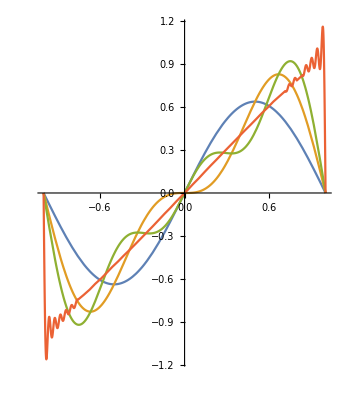

```mathematica
Plot[{S11,S12,S13,s5},{x,-1,1},AspectRatio->Automatic]
```

## 11.3 Half Ranger Expansion::



```mathematica
p11 =Plot[x^2,{x,-2,2}]
```

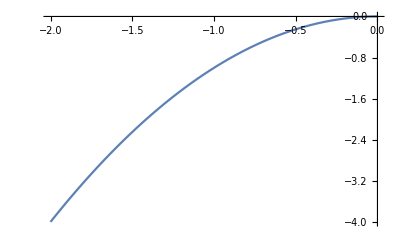

```mathematica
P12 =Plot[-x^2,{x,-2,0}]
```

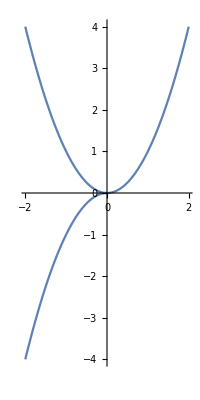

```mathematica
Show[p11,P12,AspectRatio-> Automatic,PlotRange->{-4,4}]
```

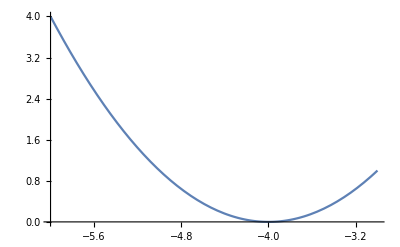

```mathematica
p3 =Plot[(x+4)^2,{x,-6,-3}]
```

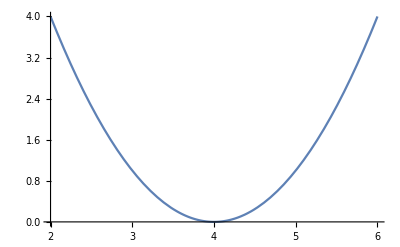

```mathematica
p4 =Plot[(x-4)^2,{x,2,6}]
```

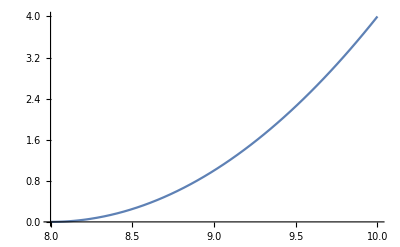

```mathematica
p6 =Plot[(x-8)^2,{x,8,10}]
```

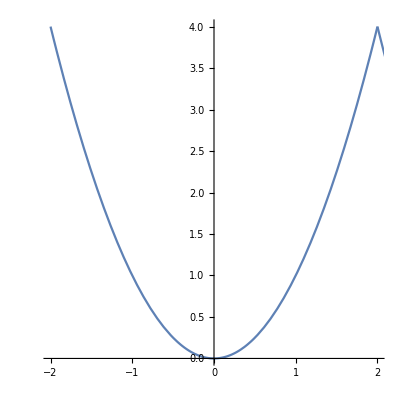

```mathematica
Show[p11,p3,p4,p6  ,AspectRatio-> Automatic]
```

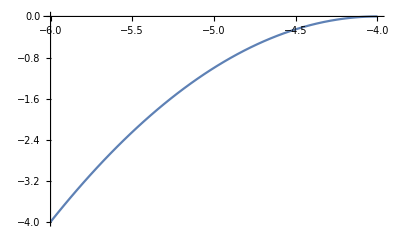

```mathematica
p7 =Plot[-(x+4)^2,{x,-6,-4}]
```

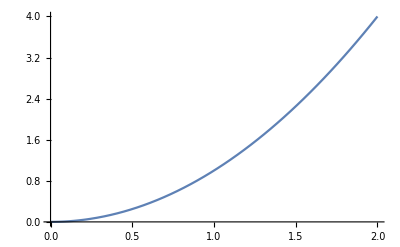

```mathematica
p8 =Plot[x^2,{x,0,2}]
```

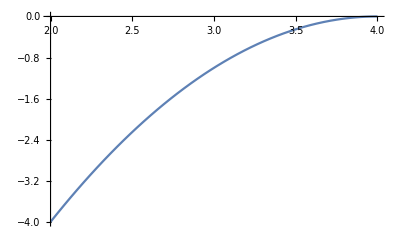

```mathematica
p9 =Plot[-(x-4)^2,{x,2,4}]
```

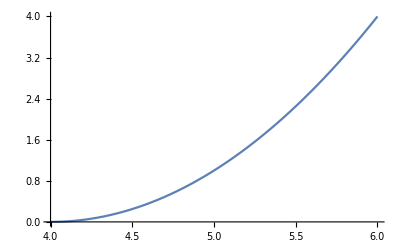

```mathematica
p10 =Plot[(x-4)^2,{x,4,6}]
```

```mathematica
Show[p6,p7,p8,p9,p10]
```

-Graphics-

```mathematica
bn2 =2/2 Integrate[x^2 Sin[n Pi x/2],{x,0,2}]
```

-(8 (2+(-2+n^2 π^2) Cos[n π]-2 n π Sin[n π]))/(n^3 π^3)

```mathematica
s2 =Sum[bn2 Sin[n Pi x/2],{n,1,7}]
```

-(8 (4-π^2) Sin[(π x)/2])/π^3-(4 Sin[π x])/π-(8 (4-9 π^2) Sin[(3 π x)/2])/(27 π^3)-(2 Sin[2 π x])/π-(8 (4-25 π^2) Sin[(5 π x)/2])/(125 π^3)-(4 Sin[3 π x])/(3 π)-(8 (4-49 π^2) Sin[(7 π x)/2])/(343 π^3)

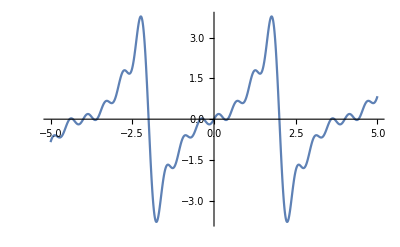

```mathematica
P21 =Plot[s2,{x,-5,5}]
```

## 11.4 Rectipter::

```mathematica
a11 = 1/Pi Integrate[Sin[t],{t,0,Pi}]
```

2/π

```mathematica
an11 =Simplify[2/Pi Integrate[Sin[t] Cos[n t],{t,0,Pi}]]
```

(2 (1+Cos[n π]))/(π-n^2 π)

```mathematica
a21 =2/Pi Integrate[Sin[t]Cos[t],{t,0,Pi}]
```

0

```mathematica
s3 =a11+a21 Cos[t]+Sum[an11 Cos[n t],{n,2,3}]
```

2/π-(4 Cos[2 t])/(3 π)

```mathematica
s7=a11+a21 Cos[t]+Sum[an11 Cos[n t],{n,2,7}]
```

2/π-(4 Cos[2 t])/(3 π)-(4 Cos[4 t])/(15 π)-(4 Cos[6 t])/(35 π)

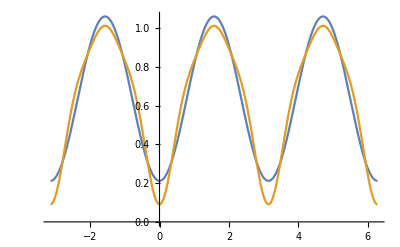

```mathematica
P =Plot[{s3,s7},{t,-Pi,2Pi}]
```

```mathematica
pg =Plot3D[Abs[Sin[t]],{t,-Pi,2Pi}]
```

Plot3D[Abs[Sin[t]],{t,-π,2 π}]

```mathematica
Show[P,pg,AspectRatio-> Automatic]
```

Show::gcomb: Could not combine the graphics objects in Show[,Plot3D[Abs[Sin[t]],{t,-π,2 π}],AspectRatio→Automatic].

## 11.5 Trigonometric Approximation ,Minimum Square Error::

```mathematica
an21 = 1/Pi Integrate[1 Cos[n x],{x,-Pi/2,Pi/2}]
```

(2 Sin[(n π)/2])/(n π)

```mathematica
Emin =Table[Integrate[1,{x,-Pi/2,Pi/2}]-Pi(2(1/2)^2 +Sum[N[an21^2],{n,1,10M}]),{M,1,25}]
```

{0.0634527,0.0318046,0.0212128,0.0159122,0.0127307,0.0106093,0.00909395,0.00795733,0.00707326,0.00636599,0.00578729,0.00530504,0.00489698,0.00454721,0.00424407,0.00397882,0.00374478,0.00353674,0.0033506,0.00318307,0.0030315,0.00289371,0.00276789,0.00265257,0.00254647}

```mathematica
(*Done*)
```